```mathematica
ClearAll["Global`*"]
```

## Mathieu equation:

## Daughter equation:

```mathematica
floquetMu[k_?NumericQ,q_?NumericQ]:=Abs[Im[MathieuCharacteristicExponent[k^2+2*q,-q]]];

kMax=10;
qMax=50;

stabilityChart=DensityPlot[floquetMu[k,q],{k,0,kMax},{q,0,qMax},PlotPoints->150,MaxRecursion->2,ColorFunction->"SunsetColors",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"Re[μ_k]"],Frame->True,FrameLabel->{"Comoving Momentum (k/m)","Resonance Parameter (q)"},PlotLabel->"Instability Bands (Re[μ_k] > 0)"];

(*Display the chart*)
Print[stabilityChart]
```

-Graphics-

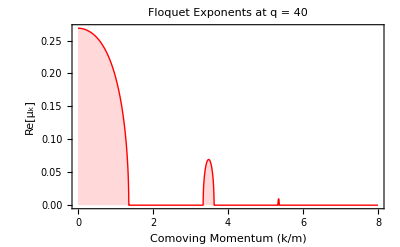

```mathematica
qSlice=40;
slicePlot=Plot[floquetMu[k,qSlice],{k,0,8},PlotRange->All,PlotPoints->200,MaxRecursion->3,Filling->Axis,FillingStyle->LightRed,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Comoving Momentum (k/m)","Re[μ_k]"},PlotLabel->StringForm["Floquet Exponents at q = ``",qSlice]];

Print[slicePlot]
```